```mathematica
<< "/Users/oliviercroissant/Documents/Math/NumericalIntegration.m"
```

```mathematica
<< "/Users/oliviercroissant/Documents/Math/BS.m"
```

```mathematica
<< "/Users/oliviercroissant/Documents/Math/SABR.m"
```

```mathematica
<< "/Users/oliviercroissant/Documents/Math/Heston_Definitif5.m"
```

```mathematica
<<"MultivariateStatistics`"
```

```mathematica
<<"ErrorBarPlots`"
```

```mathematica
Directory[]
```

/Users/oliviercroissant

```mathematica
Off[General::"spell"]
```

```mathematica
Fonctions utiles
```

```mathematica
Performs the integral : ∫_0^x ⅇ^(-a^2 s^2-b^2/s^2)ⅆs=GIntegralAnalytical[a,b,x]
```

```mathematica
GIntegralAnalytical[a1_,b1_,x1_]:=Module[{a,b,x},
x=Abs[x1];
b=Abs[b1];
a=Abs[a1];
Re[If[Abs[a]>0.001,Sign[x1]((√π)/(4a)(ⅇ^(- 2a  b)  (1-ⅇ^(4  a b)+ⅇ^(4  a b) Erf[b/x+a x]-Erf[b/x-a x]))),
Sign[x1]((-b √π+ⅇ^(-b^2/x^2) x+b √π Erf[b/x])+1/3 (-ⅇ^(-b^2/x^2) (2 b^3 ⅇ^(b^2/x^2) √π-2 b^2 x+x^3)+2 b^3 √π Erf[b/x]) a^2+1/30 ⅇ^(-b^2/x^2) (-4 b^5 ⅇ^(b^2/x^2) √π+4 b^4 x-2 b^2 x^3+3 x^5+4 b^5 ⅇ^(b^2/x^2) √π Erf[b/x]) a^4)
]]]
```

```mathematica
If we use the No function defined by  No[x]:=1/2 Erf[x/(√2)]+1/2
```

```mathematica
the ATM is caracterized by : b1=0
```

```mathematica
Implementation of GIntegralAnalytical  using NormalCDF function
```

```mathematica
GIntegralAnalytical1[a1_,b1_,x1_]:=Module[{a,b,x},
x=Abs[x1];
b=Abs[b1];
a=Abs[a1];
Re[If[Abs[a]>0.001,Sign[x1](ⅇ^(-2 a b) √π (1-ⅇ^(4 a b)-NormalCDF[√2 (b/x-a x)]+ⅇ^(4 a b) NormalCDF[√2 (b/x+a x)]))/(2 a),
Sign[x1]/30 (ⅇ^(-b^2/x^2) x (30+10 a^2 (2 b^2-x^2)+a^4 (4 b^4-2 b^2 x^2+3 x^4))+4 b (15+10 a^2 b^2+2 a^4 b^4) √π (-1+NormalCDF[(√2 b)/x]))
]]]
```

```mathematica
Computes  ∫_A^B r^γ/(√(r^2- r G +F))ⅆr
```

```mathematica
BiSABRIntegral[A_,B_,G_,F_,γ_]:=Module[{r},

 Print["A=",A," B=",B," G=",G," F=",F," γ=",γ," roots=",NSolve[r^2- r G +F==0,r],
" X1=",AppellF1[1+γ,1/2,1/2,2+γ,(2 A)/(G-√(-4 F+G^2)),(2 A)/(G+√(-4 F+G^2))],
" X2=",AppellF1[1+γ,1/2,1/2,2+γ,(2 B)/(G-√(-4 F+G^2)),(2 B)/(G+√(-4 F+G^2))]];


1/(√F  (1+γ))(-A^(1+γ)  AppellF1[1+γ,1/2,1/2,2+γ,(2 A)/(G-√(-4 F+G^2)),(2 A)/(G+√(-4 F+G^2))]+B^(1+γ)  AppellF1[1+γ,1/2,1/2,2+γ,(2 B)/(G-√(-4 F+G^2)),(2 B)/(G+√(-4 F+G^2))])]
```

```mathematica
BiSABRIntegral[A_,B_,G_,F_,γ_]:=Module[{legendrelst=LegendreCoeffs[10]},BiSABRIntegralN[A,B,G,F,γ,legendrelst]]
```

```mathematica
BiSABRIntegralN[A_,B_,G_,F_,γ_,legendrelst_]:=Module[{},
CoeffBasedIntegrate[(#^γ/(√(#^2- #G +F)))&,LegendreCoeffsFromLegendre[legendrelst,A,B]]
]
```

```mathematica
Module[{A=1.2,B=3.5,F=3.4,G=0.9,γ=0.54,legendrelst=LegendreCoeffs[10]},{
BiSABRIntegralN[A,B,G,F,γ,legendrelst],BiSABRIntegral[A,B,G,F,γ]}]
```

{1.36681,1.36681+0. ⅈ}

```mathematica
"A="0.1445206290517883" B="0.14883523895735173" G="0.24226344208464132" F="0.022926396629179044" γ="0.6666666666666667
```

```mathematica
Computation of :
```

```mathematica
Module[{A=0.1445206290517883,B=0.14883523895735173,F=0.022926396629179044,G=0.24226344208464132,γ=0.66666666666666674,legendrelst=LegendreCoeffs[10]},{
BiSABRIntegralN[A,B,G,F,γ,legendrelst],BiSABRIntegral[A,B,G,F,γ]}]
```

A=0.144521 B=0.148835 G=0.242263 F=0.0229264 γ=0.666667 roots={{r$4102→0.121132-0.0908488 ⅈ},{r$4102→0.121132+0.0908488 ⅈ}} X1=1.5126423159212+0. ⅈ X2=1.5170278437152+0. ⅈ

{0.0127145,0.0127145+0. ⅈ}

```mathematica
Module[{A=0.1445206290517883,B=0.14883523895735173,F=0.022926396629179044,G=0.24226344208464132,γ=0.66666666666666674},Plot[r^γ/(√(r^2- r G +F)),{r,A,B}]]
```

⁃Graphics⁃

```mathematica
z=1/(ϵ α) ∫_K^f 1/C[s] ⅆs  ;b1=C'[f];b2=C''[f]C[f]+b1^2;B0Bαz=C[K]C[f]
```

```mathematica
with
```

```mathematica
C[f]=(√((f+F2)^(2 β1) α1^2+F2^(2 β2) α2^2-2 (f+F2)^β1 F2^β2 α1 α2 ρs))/(√(F1^(2 β1) α1^2+F2^(2 β2) α2^2-2 F1^β1 F2^β2 α1 α2 ρs))
```

```mathematica
BiSABRIntegral[A_,B_,G_,F_,γ_]  computes  ∫_A^B r^γ/(√(r^2- r G +F))ⅆr ;  so ...
```

```mathematica
BiSABRz[K_,F1_,F2_,α1_,α2_,ρs_,β1_,β2_]:=1/(α1 β1)BiSABRIntegral[(K+F2)^β1,(F1)^β1,(2  F2^β2  α2 ρs)/α1,F2^(2 β2) (α2/α1)^2,(1-β1)/β1]
```

```mathematica
BiSABRz[K_,F1_,F2_,α1_,α2_,ρs_,β1_,β2_,legendrelst_]:=1/(α1 β1)BiSABRIntegralN[(K+F2)^β1,(F1)^β1,(2  F2^β2  α2 ρs)/α1,F2^(2 β2) (α2/α1)^2,(1-β1)/β1,legendrelst]
```

```mathematica
Module[{K=-0.1,F1=0.0418,F2=0.00728,α1=0.0435,α2=0.041402972188513,ρs=0.808,β1=0.6,β2=0.7},
BiSABRz[K,F1,F2,α1,α2,ρs,β1,β2]
]
```

0.150625-2.42599 ⅈ

```mathematica
Csabr[f_,F1_,α1_,β1_,F2_,α2_,β2_,ρs_]:=(√((f+F2)^(2 β1) α1^2+F2^(2 β2) α2^2-2 (f+F2)^β1 F2^β2 α1 α2 ρs))/(√(F1^(2 β1) α1^2+F2^(2 β2) α2^2-2 F1^β1 F2^β2 α1 α2 ρs))
```

```mathematica
Module[{K=-0.1,F1=0.0418,F2=0.00728,α1=0.0435,α2=0.041402972188513,ρs=0.808,β1=0.6,β2=0.7,f},
f=F1-F2;
Plot[1/Csabr[fx,F1,α1,β1,F2,α2,β2,ρs],{fx,K-0.01,f}]
]
```

Plot::plnr: 1/Csabr[fx, F1$3792295, α1$3792295, β1$3792295, F2$3792295, α2$3792295, β2$3792295, ρs$3792295] is not a machine-size real number at fx = -0.11. Plus…

Plot::plnr: 1/Csabr[fx, F1$3792295, α1$3792295, β1$3792295, F2$3792295, α2$3792295, β2$3792295, ρs$3792295] is not a machine-size real number at fx = -0.104137. Plus…

Plot::plnr: 1/Csabr[fx, F1$3792295, α1$3792295, β1$3792295, F2$3792295, α2$3792295, β2$3792295, ρs$3792295] is not a machine-size real number at fx = -0.0977434. Plus…

General::stop: Further output of Plot :: "plnr" will be suppressed during this calculation. Plus…

⁃Graphics⁃

```mathematica
Definition of AppellF1
```

AppellF1[a,b_1,b_2,c,z_1,z_2]==∑_(k=0)^∞ ∑_(l=0)^∞ (Pochhammer[a,k+l] Pochhammer[b_1,k] Pochhammer[b_2,l] z_1^k z_2^l)/(Pochhammer[c,k+l] k! l!)/;Abs[z_1]<1∧Abs[z_2]<1

```mathematica
low order development
```

AppellF1[a,b_1,b_2,c,z_1,z_2]==1+(a b_1 z_1)/c+(a (1+a) b_1 (1+b_1) z_1^2)/(2 c (1+c))+(a b_2 z_2)/c+(a (1+a) b_1 b_2 z_1 z_2)/(c (1+c))+(a (1+a) (2+a) b_1 (1+b_1) b_2 z_1^2 z_2)/(2 c (1+c) (2+c))+(a (1+a) b_2 (1+b_2) z_2^2)/(2 c (1+c))+(a (1+a) (2+a) b_1 b_2 (1+b_2) z_1 z_2^2)/(2 c (1+c) (2+c))+(a (1+a) (2+a) (3+a) b_1 (1+b_1) b_2 (1+b_2) z_1^2 z_2^2)/(4 c (1+c) (2+c) (3+c))+…/;Abs[z_1]<1∧Abs[z_2]<1

```mathematica
general development
```

AppellF1[a,b_1,b_2,c,z_1,z_2]==Gamma[c]/(Gamma[a]Gamma[b_1]Gamma[b_2])∑_(k=0)^∞ ∑_(j=0)^∞ Residue[(Gamma[a-s-t]Gamma[s]Gamma[b_1-s] Gamma[t]Gamma[b_2-t])/Gamma[c-s-t](-z_1)^-s(-z_2)^-t,{s,-j},{t,-k}]

```mathematica
Integral representation
```

AppellF1[a,b_1,b_2,c,z_1,z_2]==Gamma[c]/(Gamma[a] Gamma[c-a])∫_0^1 t^(a-1) (1-t)^(c-a-1) (1-t z_1)^-b_1 (1-t z_2)^-b_2ⅆt/;Re[a]>0∧Re[c-a]>0

```mathematica
Differential equation followed
```

((1-z_1) z_1 ∂_{z_1,2} w[z_1,z_2]+(1-z_1) z_2 ∂_(z_1,z_2) w[z_1,z_2]+(c-(a+b_1+1) z_1) ∂_z_1 w[z_1,z_2]-b_1 z_2 ∂_z_2 w[z_1,z_2]-a b_1 w[z_1,z_2]==0∧(1-z_2) z_2 ∂_{z_2,2} w[z_1,z_2]+z_1 (1-z_2) ∂_(z_1,z_2) w[z_1,z_2]-b_2 z_1 ∂_z_1 w[z_1,z_2]+(c-(a+b_2+1) z_2) ∂_z_2 w[z_1,z_2]-a b_2 w[z_1,z_2]==0)/; w[z_1,z_2]==AppellF1[a,b_1,b_2,c,z_1,z_2]

```mathematica
Integral and differential
```

∫AppellF1[a,b_1,b_2,c,𝒶 z_1,z_2]ⅆ z_1==(c-1)/(𝒶(a-1) (b_1-1))AppellF1[a-1,b_1-1,b_2,c-1,𝒶 z_1,z_2]

∂_{z_1,n} AppellF1[a,b_1,b_2,c,z_1,z_2]==(Pochhammer[a,n] Pochhammer[b_1,n])/Pochhammer[c,n] AppellF1[a+n,b_1+n,b_2,c+n,z_1,z_2]/;n∈Integers∧n>0

```mathematica
Formule asymptotiques
```

AppellF1[a,b_1,b_2,c,z_1,z_2]==(Gamma[c]Gamma[b_1-a])/(Gamma[c-a] Gamma[b_1])(-z_1)^-a AppellF1[a,1+a-c,b_2,1+a-b_1,1/z_1,z_2/z_1]+Gamma[c]/Gamma[a](-z_1)^-b_1 ∑_(k=0)^∞ (Gamma[a-b_1+k]Pochhammer[b_2,k])/(k! Gamma[c-b_1+k]) Hypergeometric2F1[b_1,1-c+b_1-k,1-a+b_1-k,1/z_1] z_2^k

AppellF1[a,b_1,b_2,c,z_1,z_2]==(Gamma[c]Gamma[b_1-a])/(Gamma[c-a] Gamma[b_1])(-z_1)^-a AppellF1[a,b_2,1+a-c,1+a-b_1,z_2/z_1,1/z_1]+(Gamma[c]Gamma[a-b_1])/(Gamma[a] Gamma[c-b_1])(-z_1)^-b_1(((a-b_1)^2 b_2)/(c-b_1)^2 z_2 HypergeometricPFQ[{{a-b_1+1,b_2+1},{b_1},{a-b_1+1,1}},{{c-b_1+1,2},{},{c-b_1+1}},z_2/z_1,z_2]+HypergeometricPFQ[{{b_1},{b_2,a-b_1},{1-c+b_1,1}},{{1},{c-b_1},{1-a+b_1}},z_2/z_1,1/z_1])

AppellF1[a,b_1,b_2,c,z_1,z_2]∝(Gamma[c]Gamma[b_1-a])/(Gamma[c-a] Gamma[b_1])(-z_1)^-a(1+O[1/z_1])+(Gamma[c]Gamma[a-b_1])/(Gamma[c-b_1]Gamma[a])(-z_1)^-b_1(1+O[1/z_1])/;(Abs[z_1]→∞)∧a≠b

```mathematica
Implementation of AppellF1
```

```mathematica
HypergeometricAppellF1[a_,b1_,b2_,c_,x_,y_,Nb_]:=Module[{i,j,sumtotale,currentterm,firstTerm,amnfirst,nx,cmnfirst,my,amn,cmn,b1n,b2m},
currentterm=1;nx=1;my=1;b2m=b2;firstTerm=1;b1n=b1;
sumtotale=0;amnfirst=a;cmnfirst=c;
Do[
currentterm=firstTerm;
b2m=b2;
amn=amnfirst;
cmn=cmnfirst;
my=1;
Do[sumtotale+=currentterm;currentterm*=amn b2m y/cmn/my;
(*
Print["i=",i," j=",j," currentterm=",currentterm," sumtotal=",sumtotale];
*)
amn++;b2m++;cmn++;my++;,{j,1,Nb}];
firstTerm*=x amnfirst b1n/cmnfirst/nx;
amnfirst++;cmnfirst++;b1n++;nx++;
,{i,1,Nb}];
sumtotale]
```

```mathematica
HypergeometricAppellF1Version1[a_,b1_,b2_,c_,z1_,z2_,Nb_]:=Module[{},
(1-z1)^(-b1)(1-z2)^(-b2)HypergeometricAppellF1[c-a,b1,b2,c,z1/(z1-1),z2/(z2-1),Nb]
]
```

```mathematica
HypergeometricAppellF1Version2[a_,b1_,b2_,c_,z1_,z2_,Nb_]:=Module[{},
(1-z1)^(-a)HypergeometricAppellF1[a,c-b1-b2,b2,c,z1/(z1-1),(z1-z2)/(z2-1),Nb]
]
```

```mathematica
HypergeometricAppellF1Version3[a_,b1_,b2_,c_,z1_,z2_,Nb_]:=Module[{},
(1-z2)^(-a)HypergeometricAppellF1[a,c-b1-b2,b2,c,(z2-z1)/(z1-1),z2/(z2-1),Nb]
]
```

```mathematica
HypergeometricAppellF1Version4[a_,b1_,b2_,c_,z1_,z2_,Nb_]:=Module[{},
(1-z1)^(c-a-b1)(1-z2)^(-b2)HypergeometricAppellF1[c-a,c-b1-b2,b2,c,z1,(z1-z2)/(z2-1),Nb]
]
```

```mathematica
HypergeometricAppellF1Version5[a_,b1_,b2_,c_,z1_,z2_,Nb_]:=Module[{},
(1-z1)^(-b1)(1-z2)^(c-a-b2)HypergeometricAppellF1[c-a,c-b1-b2,b2,c,(z1-z2)/(z1-1),z2,Nb]
]
```

```mathematica
Module[{a=1.4285714285714,b1=0.5,b2=0.5,c=2.4285714285714,z1=1.1737504870683+ⅈ 0.88031286530120,z2=1.1737504870683-ⅈ 0.88031286530120,Nb=150},
{HypergeometricAppellF1Version1[a,b1,b2,c,z1,z2,Nb],
HypergeometricAppellF1Version2[a,b1,b2,c,z1,z2,Nb],
HypergeometricAppellF1Version3[a,b1,b2,c,z1,z2,Nb],
,HypergeometricAppellF1Version4[a,b1,b2,c,z1,z2,Nb],
HypergeometricAppellF1Version5[a,b1,b2,c,z1,z2,Nb]}]
```

{8.19125×10^57+6.96898×10^41 ⅈ,6.59849×10^72+1.43861×10^71 ⅈ,6.61825×10^72-1.82686×10^71 ⅈ,Null,-5.76809×10^63-4.6784×10^64 ⅈ,-1.84154×10^64-1.38627×10^65 ⅈ}

```mathematica
Collect[HypergeometricAppellF1[a,Subscript[b, 1],Subscript[b, 2],c,x,y,4],x]
```

1+(a y b_2)/c+(a (1+a) y^2 b_2 (1+b_2))/(2 c (1+c))+(a (1+a) (2+a) y^3 b_2 (1+b_2) (2+b_2))/(6 c (1+c) (2+c))+x ((a b_1)/c+(a (1+a) y b_1 b_2)/(c (1+c))+(a (1+a) (2+a) y^2 b_1 b_2 (1+b_2))/(2 c (1+c) (2+c))+(a (1+a) (2+a) (3+a) y^3 b_1 b_2 (1+b_2) (2+b_2))/(6 c (1+c) (2+c) (3+c)))+x^2 ((a (1+a) b_1 (1+b_1))/(2 c (1+c))+(a (1+a) (2+a) y b_1 (1+b_1) b_2)/(2 c (1+c) (2+c))+(a (1+a) (2+a) (3+a) y^2 b_1 (1+b_1) b_2 (1+b_2))/(4 c (1+c) (2+c) (3+c))+(a (1+a) (2+a) (3+a) (4+a) y^3 b_1 (1+b_1) b_2 (1+b_2) (2+b_2))/(12 c (1+c) (2+c) (3+c) (4+c)))+x^3 ((a (1+a) (2+a) b_1 (1+b_1) (2+b_1))/(6 c (1+c) (2+c))+(a (1+a) (2+a) (3+a) y b_1 (1+b_1) (2+b_1) b_2)/(6 c (1+c) (2+c) (3+c))+(a (1+a) (2+a) (3+a) (4+a) y^2 b_1 (1+b_1) (2+b_1) b_2 (1+b_2))/(12 c (1+c) (2+c) (3+c) (4+c))+(a (1+a) (2+a) (3+a) (4+a) (5+a) y^3 b_1 (1+b_1) (2+b_1) b_2 (1+b_2) (2+b_2))/(36 c (1+c) (2+c) (3+c) (4+c) (5+c)))

```mathematica
HypergeometricAppellF1[1.4285714285714,0.50000000000000,0.50000000000000,2.4285714285714,
1.1737504870683+ⅈ 0.88031286530120,1.1737504870683-ⅈ \
0.88031286530120,150]
```

1.11846×10^45+3.16913×10^30 ⅈ

```mathematica
AppellF1[1.1,2.09,3.7,4.12,0.19-0.5 ⅈ,0.9]
```

6.6165-5.87146 ⅈ

```mathematica
AppellF1[1.4285714285714,0.50000000000000,0.50000000000000,2.4285714285714,
1.1737504870683+ⅈ 0.88031286530120,1.1737504870683-ⅈ 0.88031286530120]
```

1.43017+0. ⅈ

```mathematica
√(0.19098042207655^2-4 0.014247469381460)
```

0.+0.143235 ⅈ

```mathematica
z1=1.1737504870683+ⅈ 0.88031286530120;z2=1.1737504870683-ⅈ 0.88031286530120;
```

```mathematica
Abs[(z2-z1)/(z2-1)]
```

1.96215

```mathematica
Abs[z2]
```

1.46719

```mathematica
Abs[z2/(z2-1)]
```

1.63512

```mathematica
Power[(z2-z1)/(z2-1),10]
```

-312.101-786.207 ⅈ

```mathematica
We extend the definition of the appell function to x,y couple outside the real axis x>1 or y>1
```

AppellF1[a,b_1,b_2,c,z_1,z_2]== (1-z_1)^(c-a-b_1)(1-z_2)^-b_2 AppellF1[c-a,c-b_1-b_2,b_2,c,z_1,(z_2-z_1)/(z_2-1)]

AppellF1[a,b_1,b_2,c,z_1,z_2]== (1-z_1)^-b_1(1-z_2)^(c-a-b_2)AppellF1[c-a,b_1,c-b_1-b_2,c,(z_1-z_2)/(z_1-1),z_2]

AppellF1[a,b_1,b_2,c,z_1,z_2]== (1-z_2)^-a AppellF1[a,b_1,c-b_1-b_2,c,(z_2-z_1)/(z_2-1),z_2/(z_2-1)]/;Not[IntervalMemberQ[Interval[{1,∞}],z_1]]∧Not[IntervalMemberQ[Interval[{1,∞}],z_2]]

AppellF1[a,b_1,b_2,c,z_1,z_2]== (1-z_1)^-a AppellF1[a,c-b_1-b_2,b_2,c,z_1/(z_1-1),(z_1-z_2)/(z_1-1)]/;Not[IntervalMemberQ[Interval[{1,∞}],z_1]]∧Not[IntervalMemberQ[Interval[{1,∞}],z_2]]

AppellF1[a,b_1,b_2,c,z_1,z_2]==(1-z_1)^-b_1 (1-z_2)^-b_2 AppellF1[c-a,b_1,b_2,c,z_1/(z_1-1),z_2/(z_2-1)]/;Not[IntervalMemberQ[Interval[{1,∞}],z_1]]∧Not[IntervalMemberQ[Interval[{1,∞}],z_2]]

```mathematica
Generic Algorithm For Generic SABR
```

```mathematica
(* C[f_]:=(f+A)^β        (* this determine z,b1,b2 *) *)
```

```mathematica
(* C[f]=B[ϵ α z] determines B, so : *)
```

```mathematica
(* z=1/(ϵ α) ∫_K^f 1/C[s] ⅆs  determines z *)
(* b1=B'[z α]/B[z α]=C'[f] , b2=B''[z α]/B[z α] =C''[f]C[f]+b1^2 *)
(* SqB0Bαz represente bien sur √(B[z α]B[0])  *)
```

```mathematica
SABRgeneric5[intrinsec_,z_,b1_,b2_,zavg_,SqB0Bαz_,T_,μ_,α_,ρ_,ν_,printflag_]:=
Module[{x,I0,I1,I2,κ,f1overf0},
x=Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν;
I0=√(1+zavg ν (zavg ν-2 ρ));
I1=(zavg ν-ρ)/I0;
I2=(1-ρ^2)/I0^3;
κ=(12  μ+ (-3 b1^2 α^2+2 b2 α^2-4 z^2 μ^2-I1^2 ν^2+2 I0 I2 ν^2+6 b1 α ν ρ-16 z μ ν ρ))/(8 (1+z  ν (z  ν-2 ρ)));
f1overf0=ⅇ^(((2 μ+b1 α  ν ρ) (2 ρ ArcTan[(z  ν-ρ)/(√(1-ρ^2))]+2 ρ ArcTan[ρ/(√(1-ρ^2))]+√(1-ρ^2) Log[1+z^2  ν^2-2 z  ν ρ]))/(4  ν^2 √(1-ρ^2)));

If[printflag>0,Print["z=",z," zavg=",zavg," x=",x," κ=",κ," f1overf0=",f1overf0]];
intrinsec+α/2 √(2/π) SqB0Bαz  f1overf0 √I0 GIntegralAnalytical[√-κ,x/(√2),√T]]
```

```mathematica
Regles pour la transcription en C++
```

```mathematica
rulesz={α1->alpha1,α2->alpha2,β1->beta1,β2->beta2,ρ1->rho1,ρ2->rho2,ν1->nu1,ν2->nu2,ρs->rhos,ρv->rhov,ρc12->rhoc12,ρc21->rhoc21,αs->alphas};
ruleszz1={X1^6->(X1SQ*X1SQ*X1SQ),X2^6->(X2SQ*X2SQ*X2SQ),X1^5->(X1*X1SQ*X1SQ),X2^5->(X2*X2SQ*X2SQ),X1^4->(X1SQ*X1SQ),X2^4->(X2SQ*X2SQ),X1^3->(X1*X1SQ),X2^3->(X2*X2SQ),α1^6->(alpha1SQ*alpha1SQ*alpha1SQ),α2^6->(alpha2SQ*alpha2SQ*alpha2SQ),α1^5->(alpha1*alpha1SQ*alpha1SQ),α2^5->(alpha2*alpha2SQ*alpha2SQ),α1^4->(alpha1SQ*alpha1SQ),α2^4->(alpha2SQ*alpha2SQ),α1^3->(alpha1*alpha1SQ),α2^3->(alpha2*alpha2SQ)};
ruleszz2={α1^2->alpha1SQ,α2^2->alpha2SQ,β1^2->beta1SQ,β2^2->beta2SQ,ρ1^2->rho1SQ,ρ2^2->rho2SQ,ν1^2->nu1SQ,ν2^2->nu2SQ,ρs^2->rhosSQ,ρv^2->rhovSQ,ρc12^2->rhoc12SQ,ρc21^2->rhoc21SQ,αs^2->alphasSQ,X1^2->X1SQ,X2^2->X2SQ,F1^2->F1SQ,F2^2->F2SQ};
```

```mathematica
CTranform[x_]:=CForm[x /.ruleszz1 /. ruleszz2 /.rulesz  ]
```

```mathematica
CTranform[2 X1^3 X2 α1^3 α2 ρs ((X1/F1)^2 α1^2 β1^2+X1/F1 α1 β1 (2 ν1 ρ1+ν2 ρc12+X2/F2 α2 β2 ρs)+ν1 (ν1+X2/F2 α2 β2 ρc21+ν2 ρv))]
```

2*Power(alpha1,3)*alpha2*rhos*Power(X1,3)*X2*
   ((alpha1SQ*beta1SQ*X1SQ)/Power(F1,2) + nu1*(nu1 + nu2*rhov + (alpha2*beta2*rhoc21*X2)/F2) + 
     (alpha1*beta1*X1*(2*nu1*rho1 + nu2*rhoc12 + (alpha2*beta2*rhos*X2)/F2))/F1)

```mathematica
Precalcul pour le spreadoption
```

```mathematica
νBiSABR1[F1_,α1_,β1_,ρ1_,ν1_,F2_,α2_,β2_,ρ2_,ν2_,ρs_,ρv_,ρc12_,ρc21_,X1_,X2_,αs_]:=Module[{term1,term2,term3},
term1=X1^4 α1^4 ((X1/F1)^2 α1^2 β1^2+ν1^2+2 X1/F1 α1 β1 ν1 ρ1);
term2=X2^4 α2^4 ((X2/F2)^2 α2^2 β2^2+ν2^2+2 X2/F2 α2 β2 ν2 ρ2);
term3=X1^2 X2^2 α1^2 α2^2 ((X1/F1)^2 α1^2 β1^2 ρs^2+(X2/F2)^2  α2^2 β2^2 ρs^2+ν1^2 ρs^2+ν2^2 ρs^2+2 X2/F2 α2 β2 (ν2 ρ2 ρs^2+ν1 ρc21 (1+ρs^2))+2 X1/F1 α1 β1 (ν1 ρ1 ρs^2+ν2 ρc12 (1+ρs^2)+X2/F2 α2 β2 ρs (1+ρs^2))+2 ν1 ν2 ρv+2 ν1 ν2 ρs^2 ρv);
term4=2 X1  X2^3 α1 α2^3 ρs (F2^(-2+2 β2) α2^2 β2^2+(F2^(-1+β2) α2 β2 (2 F1 ν2 ρ2+F1 ν1 ρc21+F1^β1 α1 β1 ρs))/F1+ν2 (ν2+X1/F1 α1 β1 ρc12+ν1 ρv));
term5=2 X1^3 X2 α1^3 α2 ρs ((X1/F1)^2 α1^2 β1^2+X1/F1 α1 β1 (2 ν1 ρ1+ν2 ρc12+X2/F2 α2 β2 ρs)+ν1 (ν1+X2/F2 α2 β2 ρc21+ν2 ρv));
(√(term1+term2+term3-term4-term5))/αs^2]
```

```mathematica
ρBiSABR1[F1_,α1_,β1_,ρ1_,ν1_,F2_,α2_,β2_,ρ2_,ν2_,ρs_,ρv_,ρc12_,ρc21_,X1_,X2_,αs_,νs_]:=Module[{},
(X1^3 α1^3 ((X1 α1 β1)/F1+ν1 ρ1)-X2^3 α2^3 ((X2 α2 β2)/F2+ν2 ρ2)-X1^2 X2 α1^2 α2 (ρs ((2 X1 α1 β1)/F1+ν2 ρc12+(X2 α2 β2 ρs)/F2)+ν1 (ρc21+ρ1 ρs))+X1 X2^2 α1 α2^2 (ρs ((2 X2 α2 β2)/F2+ν1 ρc21+(X1 α1 β1 ρs)/F1)+ν2 (ρc12+ρ2 ρs)))/(νs αs^3)]
```

```mathematica
Module[{F1 =0.040908314711852,alpha1= 0.013242339206841,beta1 =0.40000000000000,rho1= 0.35242800000000,nu1 =0.25283800000000,
F2= 0.044141630651630,alpha2 =0.014300324948643,beta2= 0.40000000000000,rho2= 0.37737400000000,nu2= 0.23093200000000,
rhos =0.90400000000000,rhov= 0.60000000000000,rhoc12=-0.050000000000000,rhoc21=-0.050000000000000,X1 =0.27843551868880,X2= 0.28703796939008,
alphas= 0.0017550658859387,nus =0.25040352068222},
νBiSABR1[F1,alpha1,beta1,rho1,nu1,F2,alpha2,beta2,rho2,nu2,rhos,rhov,rhoc12,rhoc21,X1,X2,alphas]]
```

0.250404

```mathematica
Module[{F1 =0.040908314711852,alpha1= 0.013242339206841,beta1 =0.40000000000000,rho1= 0.35242800000000,nu1 =0.25283800000000,
F2= 0.044141630651630,alpha2 =0.014300324948643,beta2= 0.40000000000000,rho2= 0.37737400000000,nu2= 0.23093200000000,
rhos =0.90400000000000,rhov= 0.60000000000000,rhoc12=-0.050000000000000,rhoc21=-0.050000000000000,X1 =0.27843551868880,X2= 0.28703796939008,
alphas= 0.0017550658859387,nus =0.25040352068222},
ρBiSABR1[F1,alpha1,beta1,rho1,nu1,F2,alpha2,beta2,rho2,nu2,rhos,rhov,rhoc12,rhoc21,X1,X2,alphas,nus]]
```

-1.028

```mathematica
CTranform[X1^2 X2^2 F2  α1^2 α2^2 (X1^2 F2 α1^2 β1 (-1+2 β1+(-2+β1) ρs^2)+2 X1 F1 α1 (-F1 β2 ν2 ρ2 ρs+F2 β1 (ν2 ρc12 (-1+ρs^2)+ν1 ρ1 (2+ρs^2)))-F1^2 F2 (-1+ρs^2) (ν1^2+ν2^2-2 ν1 ν2 ρv))]
```

alpha1SQ*alpha2SQ*F2*X1SQ*(-(F1SQ*F2*(-1 + rhosSQ)*(nu1SQ + nu2SQ - 2*nu1*nu2*rhov)) + 
     2*alpha1*F1*(-(beta2*F1*nu2*rho2*rhos) + beta1*F2*(nu2*rhoc12*(-1 + rhosSQ) + nu1*rho1*(2 + rhosSQ)))*X1 + 
     alpha1SQ*beta1*F2*(-1 + 2*beta1 + (-2 + beta1)*rhosSQ)*X1SQ)*X2SQ

```mathematica
μBiSABR1[F1_,α1_,β1_,ρ1_,ν1_,F2_,α2_,β2_,ρ2_,ν2_,ρs_,ρv_,ρc12_,ρc21_,X1_,X2_,αs_]:=Module[{term1,term2,term3,term4},
term1=F1^2 X2^6 α2^6 (-1+β2) β2+X1^5 F2^2 α1^5 β1 (X1 α1 (-1+β1)+2 F1 ν1 ρ1);
term2=-3 X1^4 X2 F2^2 α1^4 α2 β1 (X1 α1 (-1+β1)+2 F1 ν1 ρ1) ρs+F1^2 X2^5 α2^5 β2 (2 F2 ν2 ρ2-3 X1 α1 (-1+β2) ρs)+X1 F1^2 X2^4 α1 α2^4 β2 (-6 F2 ν2 ρ2 ρs+X1 α1 (-1+2 β2+(-2+β2) ρs^2));
term3=X1^2 X2^3 α1^2 α2^3 (X1 α1 ρs (-F2^2 (-1+β1) β1-F1^2 (-1+β2) β2+2 F1 F2 β1 β2 (-1+ρs^2))+2 F1 F2 (-F2 β1 ν1 ρ1 ρs+F1 β2 (ν1 ρc21 (-1+ρs^2)+ν2 ρ2 (2+ρs^2))));
term4=X1^2 X2^2 F2  α1^2 α2^2 (X1^2 F2 α1^2 β1 (-1+2 β1+(-2+β1) ρs^2)+2 X1 F1 α1 (-F1 β2 ν2 ρ2 ρs+F2 β1 (ν2 ρc12 (-1+ρs^2)+ν1 ρ1 (2+ρs^2)))-F1^2 F2 (-1+ρs^2) (ν1^2+ν2^2-2 ν1 ν2 ρv));
(term1+term2+term3+term4)/(2 F1^2 F2^2 αs^3)]
```

```mathematica
Simplify[Normal[Series[(√((s+F2)^(2 β1) α1^2+X2^2 α2^2-2 (s+F2)^β1 X2 α1 α2 ρs))/αs,{s,F2,2}]]]
```

(-2^β1 F2^(-1+β1) (F2-s) α1 β1 (2^β1 F2^β1 α1-X2 α2 ρs)+2 (4^β1 F2^(2 β1) α1^2+X2^2 α2^2-2^(1+β1) F2^β1 X2 α1 α2 ρs)+(2^(-2+β1) F2^(-2+β1) (F2-s)^2 α1 β1 (8^β1 F2^(3 β1) α1^3 (-1+β1)-3 4^β1 F2^(2 β1) X2 α1^2 α2 (-1+β1) ρs-X2^3 α2^3 (-1+β1) ρs+2^β1 F2^β1 X2^2 α1 α2^2 (-1-2 ρs^2+β1 (2+ρs^2))))/(4^β1 F2^(2 β1) α1^2+X2^2 α2^2-2^(1+β1) F2^β1 X2 α1 α2 ρs))/(2 αs √(4^β1 F2^(2 β1) α1^2+X2^2 α2^2-2^(1+β1) F2^β1 X2 α1 α2 ρs))

```mathematica
BiSABRspreadC[F1_,F2_,α1_,α2_,β1_,β2_,ρs_,X1_,X2_,αs_,s_]:=Module[{},
If[Abs[s+F2]<2 10^(-3)F2,
(-2^β1 F2^(-1+β1) (F2-s) α1 β1 (2^β1 F2^β1 α1-X2 α2 ρs)+2 (4^β1 F2^(2 β1) α1^2+X2^2 α2^2-2^(1+β1) F2^β1 X2 α1 α2 ρs)+(2^(-2+β1) F2^(-2+β1) (F2-s)^2 α1 β1 (8^β1 F2^(3 β1) α1^3 (-1+β1)-3 4^β1 F2^(2 β1) X2 α1^2 α2 (-1+β1) ρs-X2^3 α2^3 (-1+β1) ρs+2^β1 F2^β1 X2^2 α1 α2^2 (-1-2 ρs^2+β1 (2+ρs^2))))/(4^β1 F2^(2 β1) α1^2+X2^2 α2^2-2^(1+β1) F2^β1 X2 α1 α2 ρs))/(2 αs √(4^β1 F2^(2 β1) α1^2+X2^2 α2^2-2^(1+β1) F2^β1 X2 α1 α2 ρs)),
(√((s+F2)^(2 β1) α1^2+X2^2 α2^2-2 (s+F2)^β1 X2 α1 α2 ρs))/αs]]
```

```mathematica
BiSABRspreadC[F1_,F2_,α1_,α2_,β1_,β2_,ρs_,X1_,X2_,αs_,s_]:=Module[{},
(√((s+F2)^(2 β1) α1^2+X2^2 α2^2-2 (s+F2)^β1 X2 α1 α2 ρs))/αs]
```

```mathematica
Series[((s+F2)^(-1+2 β1) α1^2 β1- X2 (s+F2)^(-1+β1) α1 α2 β1 ρs)/(αs √((s+F2)^(2 β1) α1^2+X2^2 α2^2-2 (s+F2)^β1 X2 α1 α2 ρs)),{s,-F2,1}]
```

((F2+s)^(-1+2 β1) α1^2 β1-(F2+s)^(-1+β1) X2 α1 α2 β1 ρs)/(αs √((F2+s)^(2 β1) α1^2+X2^2 α2^2-2 (F2+s)^β1 X2 α1 α2 ρs))

```mathematica
BiSABRspreadCderivative[F1_,F2_,α1_,α2_,β1_,β2_,ρs_,X1_,X2_,αs_,s_]:=Module[{},
((s+F2)^(-1+2 β1) α1^2 β1- X2 (s+F2)^(-1+β1) α1 α2 β1 ρs)/(αs √((s+F2)^(2 β1) α1^2+X2^2 α2^2-2 (s+F2)^β1 X2 α1 α2 ρs))]
```

```mathematica
BiSABRspreadCderivative2[F1_,F2_,α1_,α2_,β1_,β2_,ρs_,X1_,X2_,αs_,s_]:=Module[{},
((2 (s+F2)^(-1+2 β1) α1^2 β1-2 X2 (s+F2)^(-1+β1) α1 α2 β1 ρs)^2)/(4 (√((s+F2)^(2 β1) α1^2+X2^2 α2^2-2 (s+F2)^β1 X2 α1 α2 ρs))^3)+(2 (s+F2)^(-2+2 β1) α1^2 β1 (-1+2 β1)-2 F2^β2 (s+F2)^(-2+β1) α1 α2 (-1+β1) β1 ρs)/(2 √((s+F2)^(2 β1) α1^2+X2^2 α2^2-2 (s+F2)^β1 X2 α1 α2 ρs))]
```

```mathematica
Spreadoption
```

```mathematica
Utilise une integration numerique pour le calcul du z, Fait des tas d'affichage
```

```mathematica
BiSABRSpreadOption[F1_,α1_,β1_,ρ1_,ν1_,F2_,α2_,β2_,ρ2_,ν2_,K_,T_,ρs_,ρv_,ρc12_,ρc21_,legendrelst_,printflag_]:=Module[
{intrinsec,z,zb,b1,b2,SqB0Bαz,favg,zavg,Ck,αsp,νsp,ρsp,μsp,X1,X2,Qs,Q1,Q2,Qb,C1,C2,C1p,C2p,Q,COV,COV1,COV0,ρsb,ρsα1,ρsα2,ρbα1,ρbα2,N1,N2,νspZ,ρspZ},
X1=F1^β1;X2=F2^β2;αsp=√(X1^2 α1^2+X2^2 α2^2-2 X1 X2 α1 α2 ρs);
If[printflag>0,Print["X1=",X1," X2=",X2," αsp=",αsp]];
νsp=νBiSABR1[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,ρs,ρv,ρc12,ρc21,X1,X2,αsp];
ρsp=ρBiSABR1[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,ρs,ρv,ρc12,ρc21,X1,X2,αsp,νsp];
μsp=μBiSABR1[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,ρs,ρv,ρc12,ρc21,X1,X2,αsp];
z=Re[BiSABRz[K,F1,F2,α1,α2,ρs,β1,β2]];
zb=BiSABRz[K,F1,F2,α1,α2,ρs,β1,β2,legendrelst];
If[printflag>0,Print["BiSABRSpreadOption:z=",z,"zb=",zb]];
favg=(F1-F2+K)/2;
zavg=z;
b1=BiSABRspreadCderivative[F1,F2,α1,α2,β1,β2,ρs,X1,X2,αsp,favg];
Csecond=BiSABRspreadCderivative2[F1,F2,α1,α2,β1,β2,ρs,X1,X2,αsp,favg];
Cfavg=BiSABRspreadC[F1,F2,α1,α2,β1,β2,ρs,X1,X2,αsp,favg];
Ck=BiSABRspreadC[F1,F2,α1,α2,β1,β2,ρs,X1,X2,αsp,K];
b2=Csecond Cfavg+b1^2;
SqB0Bαz=√Ck;
intrinsec=Max[F1-F2-K,0];
If[printflag>0,Print["BiSABRSpreadOption:K=",K," b1:Cprime[favg]=",b1," Csecond[favg]=",Csecond, " b2=",b2," Cfavg=",Cfavg]];
If[printflag>0,Print["BiSABRSpreadOption:α=",αsp," ν=",νsp," ρ=",ρsp,"  μ=",μsp]];
If[printflag>0,Print["BiSABRSpreadOption:intrinsec Value=",intrinsec,"  z=",z," SqB0Bαz=",SqB0Bαz]];
If[printflag>0,
C1=F1^β1;C2=F2^β2;C1p=β1 F1^(β1-1);C2p=β2 F2^(β2-1);
Q=√(α1^2 C1^2+α2^2 C2^2-2ρs α1 α2 C1 C2);
Qs=α1^2 C1  C1p-α1 α2 ρs C2  C1p;
Qb=α1^2 C1 C1p-α1 α2 ρs C2  C1p-α1 α2 ρs C1 C2p+α2^2 C2 C2p;
Q1=α1 C1^2-α2 ρs C1 C2;
Q2=-α1 ρs C1 C2+α2 C2^2;
ρsb=( ρs α1 C1-  α2 C2)/Q;
ρsα1=( ρ1  α1 C1- ρc21 α2 C2)/Q;
ρsα2=(ρc12 α1 C1- ρ2 α2 C2)/Q;
ρbα1=ρc21;
ρbα2=ρ2;
COV0={
{  α1^2 C1^2,                                                          ρs α1 C1 α2  C2 ,                         ρ1  α1 C1 ν1 α1,                                    ρc12 α1 C1 ν2 α2},
{ ρs α1 C1 α2  C2 ,                                         (α2  C2)^2,                                       ρc21 α2 C2 ν1 α1,                                 ρ2 α2 C2 ν2 α2},
{ ρ1  α1 C1 ν1 α1,                                            ρc21 α2 C2 ν1  α1,                       (ν1 α1)^2,                                                ρv ν1 α1 ν2 α2},
{ ρc12 α1 C1 ν2 α2,                                        ρ2 α2  C2 ν2 α2 ,                           ρv ν1 α1 ν2 α2,                                    (ν2 α2)^2}
};
Plot[Det[{{  α1^2 C1^2,                                                          ρs α1 C1 α2  C2 ,                         ρ1  α1 C1 ν1 α1,                                    rc12 α1 C1 ν2 α2},
{ ρs α1 C1 α2  C2 ,                                         (α2  C2)^2,                                       ρc21 α2 C2 ν1 α1,                                 ρ2 α2 C2 ν2 α2},
{ ρ1  α1 C1 ν1 α1,                                            ρc21 α2 C2 ν1  α1,                       (ν1 α1)^2,                                                ρv ν1 α1 ν2 α2},
{ rc12 α1 C1 ν2 α2,                                        ρ2 α2  C2 ν2 α2 ,                           ρv ν1 α1 ν2 α2,                                    (ν2 α2)^2}}],{rc12,-1,+1}];
Plot[Det[{{  α1^2 C1^2,                                                          ρs α1 C1 α2  C2 ,                         ρ1  α1 C1 ν1 α1,                                    ρc12 α1 C1 ν2 α2},
{ ρs α1 C1 α2  C2 ,                                         (α2  C2)^2,                                       rc21 α2 C2 ν1 α1,                                 ρ2 α2 C2 ν2 α2},
{ ρ1  α1 C1 ν1 α1,                                            rc21 α2 C2 ν1  α1,                       (ν1 α1)^2,                                                ρv ν1 α1 ν2 α2},
{ ρc12 α1 C1 ν2 α2,                                        ρ2 α2  C2 ν2 α2 ,                           ρv ν1 α1 ν2 α2,                                    (ν2 α2)^2}}],{rc21,-1,+1}];
Print["Initial Eigenvalues=",Eigenvalues[COV0]];
Print["Initial Det=",Det[COV0]];
COV1={
{  α1^2 C1^2+α2^2 C2^2-2ρs α1 α2 C1 C2,       ( ρs α1 C1-  α2 C2) α2  C2 ,     ( ρ1  α1 C1- ρc21 α2 C2)ν1 α1,     (ρc12 α1 C1- ρ2 α2 C2) ν2 α2},
{( ρs α1 C1-  α2 C2) α2  C2,                       (α2  C2)^2,                                       ρc21 α2 C2 ν1 α1,                                 ρ2 α2 C2 ν2 α2},
{( ρ1  α1 C1- ρc21 α2 C2) ν1  α1,             ρc21 α2 C2 ν1  α1,                       (ν1 α1)^2,                                                ρv ν1 α1 ν2 α2},
{(ρc12 α1 C1- ρ2 α2 C2) ν2 α2,                ρ2 α2  C2 ν2 α2 ,                           ρv ν1 α1 ν2 α2,                                    (ν2 α2)^2}
};
COV={
{Q^2,ρsb Q α2  C2 ,ρsα1 Q ν1 α1,ρsα2 Q ν2 α2},
{ρsb Q α2  C2,(α2  C2)^2,ρbα1 α2 C2 ν1 α1,ρbα2 α2 C2 ν2 α2},
{ρsα1 Q ν1  α1,ρbα1 α2 C2 ν1  α1,(ν1 α1)^2,ρv ν1 α1 ν2 α2},
{ρsα2 Q ν2 α2,ρbα2 α2  C2 ν2 α2 ,ρv ν1 α1 ν2 α2,(ν2 α2)^2}
};
Print[" COV1-COV=",COV1-COV];
N1={Q,0,0,0}.(COV.{Q,0,0,0});
N2={Qs/Q,Qb/Q,Q1/Q,Q2/Q}.(COV.{Qs/Q,Qb/Q,Q1/Q,Q2/Q});
νspZ=(√N2)/Q;
ρspZ=({Q,0,0,0}.(COV.{Qs/Q,Qb/Q,Q1/Q,Q2/Q}))/√(N2 N1);
Print["BiSABRSpreadOption:N1=",N1];Print["BiSABRSpreadOption:N2=",N2];
Print["BiSABRSpreadOption:νspZ=",νspZ];Print["BiSABRSpreadOption:ρspZ=",ρspZ];
Print["BiSABRSpreadOption:ds=",{Q,0,0,0}];Print["BiSABRSpreadOption:dα_11=",{Qs/Q,Qb/Q,Q1/Q,Q2/Q}];
Print["BiSABRSpreadOption:COV=",COV];
Print["BiSABRSpreadOption:eigenvalues=",Eigenvalues[COV]];
Print["BiSABRSpreadOption: Det=",Det[COV]];
];
Re[SABRgeneric5[intrinsec,z,b1,b2,zavg,SqB0Bαz,T,μsp,αsp,ρsp,νsp,printflag]]]
```

```mathematica
On[General::"spell"]
```

```mathematica
Utilise une integration numerique pour le calcul du z
```

```mathematica
BiSABRSpreadOption[F1_,α1_,β1_,ρ1_,ν1_,F2_,α2_,β2_,ρ2_,ν2_,K_,T_,ρs_,ρv_,ρc12_,ρc21_,legendrelst_,printflag_]:=Module[
{intrinsec,z,b1,b2,SqB0Bαz,favg,zavg,Ck,αsp,νsp,ρsp,μsp,X1,X2,Qs,Q1,Q2,Qb,C1,C2,C1p,C2p,Q,COV,COV1,COV0,ρsb,ρsα1,ρsα2,ρbα1,ρbα2,N1,N2,νspZ,ρspZ},
X1=F1^β1;X2=F2^β2;αsp=√(X1^2 α1^2+X2^2 α2^2-2 X1 X2 α1 α2 ρs);
νsp=νBiSABR1[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,ρs,ρv,ρc12,ρc21,X1,X2,αsp];
ρsp=ρBiSABR1[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,ρs,ρv,ρc12,ρc21,X1,X2,αsp,νsp];
μsp=μBiSABR1[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,ρs,ρv,ρc12,ρc21,X1,X2,αsp];
z=BiSABRz[K,F1,F2,α1,α2,ρs,β1,β2,legendrelst];
favg=(F1-F2+K)/2;
zavg=BiSABRz[favg,F1,F2,α1,α2,ρs,β1,β2,legendrelst];
b1=BiSABRspreadCderivative[F1,F2,α1,α2,β1,β2,ρs,X1,X2,αsp,favg];
Csecond=BiSABRspreadCderivative2[F1,F2,α1,α2,β1,β2,ρs,X1,X2,αsp,favg];
Cfavg=BiSABRspreadC[F1,F2,α1,α2,β1,β2,ρs,X1,X2,αsp,favg];
Ck=BiSABRspreadC[F1,F2,α1,α2,β1,β2,ρs,X1,X2,αsp,K];
b2=Csecond Cfavg+b1^2;
SqB0Bαz=√Ck;
intrinsec=Max[F1-F2-K,0];
If[printflag==10,Print["BiSABRSpreadOption:X1=",X1," X2=",X2," z=",z]];
If[printflag==10,Print["BiSABRSpreadOption:b1=",b1," b2=",b2," SqB0Bαz=",SqB0Bαz]];
If[printflag==10,Print["BiSABRSpreadOption:α=",αsp," ν=",νsp," ρ=",ρsp,"  μ=",μsp]];
res=SABRgeneric5[intrinsec,z,b1,b2,zavg,SqB0Bαz,T,μsp,αsp,ρsp,νsp,printflag];
If[printflag==10,Print["BiSABRSpreadOption:res=",res]];
Re[res]]
```

```mathematica
BiSABRSpreadOptionVol[F1_,α1_,β1_,ρ1_,ν1_,F2_,α2_,β2_,ρ2_,ν2_,K_,T_,ρs_,ρv_,ρc12_,ρc21_,legendrelst_,printflag_]:=
NormalImplicitVol[F1-F2,K,T,BiSABRSpreadOption[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,K,T,ρs,ρv,ρc12,ρc21,legendrelst,0]]
```

```mathematica
BiSABRSpreadOptionNormalCorrelation[F1_,α1_,β1_,ρ1_,ν1_,F2_,α2_,β2_,ρ2_,ν2_,K_,T_,ρs_,ρv_,ρc12_,ρc21_,legendrelst_,printflag_]:=Module[{method="Directe",zetavmethod="Exact",zmethod="Exact",favmethod ="Arithmetic",σATMnormal1,σATMnormal2,implicitNormalvols},
{σATMnormal1,σATMnormal2}={F1 SABROption[F1,α1,β1,ρ1,ν1,{method,zmethod,zetavmethod,favmethod},F1 1.0001,T][[1]],
F2 SABROption[F2,α2,β2,ρ2,ν2,{method,zmethod,zetavmethod,favmethod},F2 1.0001,T][[1]]};
implicitNormalvols=BiSABRSpreadOptionVol[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,K,T,ρs,ρv,ρc12,ρc21,legendrelst,0];
NormalImplicitCorrelation[σATMnormal1,σATMnormal2,implicitNormalvols]]
```

```mathematica
Debiaisage (symetrisation du role S1 et S2)
```

```mathematica
BiSABRSpreadOptionCorrected[F1_,α1_,β1_,ρ1_,ν1_,F2_,α2_,β2_,ρ2_,ν2_,K_,T_,ρs_,ρv_,ρc12_,ρc21_,legendrelst_,printflag_]:=(BiSABRSpreadOption[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,K,T,ρs,ρv,ρc12,ρc21,legendrelst,printflag]+
BiSABRSpreadOption[F2,α2,β2,ρ2,ν2,F1,α1,β1,ρ1,ν1,-K,T,ρs,ρv,ρc21,ρc12,legendrelst,printflag]+F1-F2-K)/2
```

```mathematica
Extended BISABR spreadoption (with coefficients)
```

```mathematica
(* compute E[(a1*S1-a2*S2-K)Subscript[1, a1*S1-a2*S2-K>0]] *)
```

```mathematica
GeneralizedBiSABRSpreadOption[F1_,α1_,β1_,ρ1_,ν1_,F2_,α2_,β2_,ρ2_,ν2_,K_,T_,ρs_,ρv_,ρc12_,ρc21_,a1_,a2_,printflag_]:=Module[{},
BiSABRSpreadOption[a1 F1,α1 a1^(1-β1),β1,ρ1,ν1,a2 F2,α2 a2^(1-β2),β2,ρ2,ν2,K,T,ρs,ρv,ρc12,ρc21,printflag]
]
```

```mathematica
GeneralizedBiSABRSpreadOption[F1_,α1_,β1_,ρ1_,ν1_,F2_,α2_,β2_,ρ2_,ν2_,K_,T_,ρs_,ρv_,ρc12_,ρc21_,a1_,a2_,legendrelst_,printflag_]:=Module[{},
BiSABRSpreadOption[a1 F1,α1 a1^(1-β1),β1,ρ1,ν1,a2 F2,α2 a2^(1-β2),β2,ρ2,ν2,K,T,ρs,ρv,ρc12,ρc21,legendrelst,printflag]
]
```

```mathematica
Application numerique
```

```mathematica
TestCorrelation[ρ1_,ρ2_,ρs_,ρv_,ρc12_,ρc21_]:=Module[{},Print["Test Correlation : Eigenvalues=",Eigenvalues[{{1,ρ1,ρs,ρc12},{ρ1,1,ρc21,ρv},{ρs,ρc21,1,ρ2},{ρc12,ρv,ρ2,1}}]]];
```

```mathematica
Simple execution
```

```mathematica
Module[{
F1=0.0418,
α1=0.0435,
β1=0.6,
ρ1=-0.1819,
ν1=0.3798,
F2=0.0363,
α2=0.0671,
β2=0.7,
ρ2=-0.1136,
ν2=0.3797,
T=1,
ρs=0.808,
ρv=0.,
ρc12=-0.2,
ρc21=0.,
K=-0.002,legendrelst=LegendreCoeffs[10]
},
{BiSABRSpreadOption[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,K,T,ρs,ρv,ρc12,ρc21,legendrelst,0],BiSABRSpreadOptionCorrected[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,K,T,ρs,ρv,ρc12,ρc21,legendrelst,0]}]
```

{0.00757654,0.00758945}

```mathematica
Module[{
F1=0.0418,
α1=0.0435,
β1=0.6,
ρ1=-0.1819,
ν1=0.3798,
F2=0.0363,
α2=0.0671,
β2=0.7,
ρ2=-0.1136,
ν2=0.3797,
T=10,
ρs=0.8,
ρv=0.5,
ρc12=-0.5,
ρc21=-0.,
K=0.0035,legendrelst=LegendreCoeffs[10]
},
{BiSABRSpreadOptionNormalCorrelation[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,K,T,ρs,ρv,ρc12,ρc21,legendrelst,0],BiSABRSpreadOptionVol[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,K,T,ρs,ρv,ρc12,ρc21,legendrelst,0]}]
```

{0.814766,0.00446159}

```mathematica
Smile
```

money=0.0055

Test Correlation : Eigenvalues={2.12284,1.17947,0.562149,0.135538}

σATMnormal1=0.0102202  σATMnormal2=0.0108588

implicit correlation={0.864518,0.869517,0.874367,0.879077,0.883655,0.888109,0.892449,0.896681,0.900814,0.904856,0.908813,0.912691,0.916494,0.920223,0.923877,0.927451,0.930932,0.934303,0.937539,0.940604,0.943459,0.946053,0.948332,0.950239,0.951721,0.952727,0.953226,0.953234,0.952746,0.951767,0.950314,0.948419,0.946118,0.943454,0.940469,0.937206,0.933705,0.930001,0.926126,0.922107,0.917964}

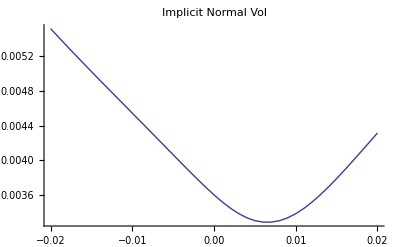
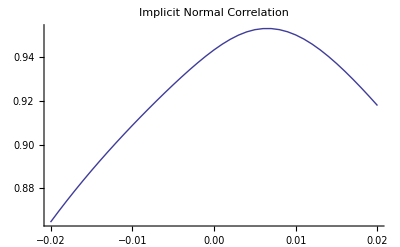
{0.18022,{-Graphics-,-Graphics-}}

```mathematica
Timing[Module[{method="Directe",zetavmethod="Exact",zmethod="Exact",favmethod="Arithmetic",F1=0.0418,α1=0.0435,β1=0.6,ρ1=-0.1819,ν1=0.3798,F2=0.0363,α2=0.0671,β2=0.7,ρ2=-0.1136,ν2=0.3797,T=30,ρs=0.8,ρv=0.5,ρc12=-0.3,ρc21=-0.3,legendrelst=LegendreCoeffs[20]},Print["money=",F1-F2];TestCorrelation[ρ1,ρ2,ρs,ρv,ρc12,ρc21];strikevalues=Table[k,{k,-0.02,0.02,0.001}];callvalues=Table[BiSABRSpreadOption[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,strikevalues⟦i⟧,T,ρs,ρv,ρc12,ρc21,legendrelst,0],{i,1,Length[strikevalues]}];implicitNormalvols=Table[NormalImplicitVol[F1-F2,strikevalues⟦i⟧,T,callvalues⟦i⟧],{i,1,Length[strikevalues]}];{σATMnormal1,σATMnormal2}={F1 SABROption[F1,α1,β1,ρ1,ν1,{method,zmethod,zetavmethod,favmethod},F1 1.0001,T]⟦1⟧,F2 SABROption[F2,α2,β2,ρ2,ν2,{method,zmethod,zetavmethod,favmethod},F2 1.0001,T]⟦1⟧};Print["σATMnormal1=",σATMnormal1,"  σATMnormal2=",σATMnormal2];implicitcorrelations=Table[NormalImplicitCorrelation[σATMnormal1,σATMnormal2,implicitNormalvols⟦i⟧],{i,1 Length[strikevalues]}];Print["implicit correlation=",implicitcorrelations];
{ListPlot[Transpose[{strikevalues,implicitNormalvols}],Joined->True,PlotLabel->"Implicit Normal Vol"],ListPlot[Transpose[{strikevalues,implicitcorrelations}],Joined->True,PlotLabel->"Implicit Normal Correlation",PlotRange->All]}]]
```

```mathematica
Nouvelle implementation basée sur normalheston
```

```mathematica
Strategie 1
```

```mathematica
BiSABRNormalHestonSpreadOption[F1_,α1_,β1_,ρ1_,ν1_,F2_,α2_,β2_,ρ2_,ν2_,K_,T_,ρs_,ρv_,ρc12_,ρc21_,printflag_]:=Module[
{intrinsec,z,b1,b2,SqB0Bαz,favg,zavg,Ck,αsp,νsp,ρsp,μsp,X1,X2,Qs,Q1,Q2,Qb,C1,C2,C1p,C2p,Q,COV,COV1,COV0,ρsb,ρsα1,ρsα2,ρbα1,ρbα2,N1,N2,νspZ,ρspZ,λ,θ,S0,κ},
X1=F1^β1;X2=F2^β2;αsp=√(X1^2 α1^2+X2^2 α2^2-2 X1 X2 α1 α2 ρs);
νsp=νBiSABR1[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,ρs,ρv,ρc12,ρc21,X1,X2,αsp];
ρsp=ρBiSABR1[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,ρs,ρv,ρc12,ρc21,X1,X2,αsp,νsp];
μsp=μBiSABR1[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,ρs,ρv,ρc12,ρc21,X1,X2,αsp];
κ=2νsp αsp;
 λ=Max[Abs[(κ^2/2-(2μsp αsp^2 +νsp^2 αsp^2 ))/αsp^2],10^(-8)] ;
  θ=Min[Abs[κ^2/(2λ)],100 Abs[αsp^2]];
 λ=(κ^2/2-(2μsp αsp^2 +νsp^2 αsp^2 ))/αsp^2;
  θ=κ^2/(2λ);
S0=F1-F2;
If[printflag>0,Print["BiSABRNormalHestonSpreadOption: λ=",λ," θ=",θ," κ=",κ," αsp=",αsp]];
HestonNormalCall[ρsp,λ,θ,κ,αsp^2,S0,K,T]]
```

```mathematica
BiSABRNormalHestonSpreadOptionComputeα[F1_,α1_,β1_,ρ1_,ν1_,F2_,α2_,β2_,ρ2_,ν2_,ρs_,ρv_,ρc12_,ρc21_,printflag_]:=Module[
{intrinsec,z,b1,b2,SqB0Bαz,favg,zavg,Ck,αsp,νsp,ρsp,μsp,X1,X2,Qs,Q1,Q2,Qb,C1,C2,C1p,C2p,Q,COV,COV1,COV0,ρsb,ρsα1,ρsα2,ρbα1,ρbα2,N1,N2,νspZ,ρspZ},
X1=F1^β1;X2=F2^β2;αsp=√(X1^2 α1^2+X2^2 α2^2-2 X1 X2 α1 α2 ρs)];
```

```mathematica
BiSABRNormalHestonSpreadOptionComputeν[F1_,α1_,β1_,ρ1_,ν1_,F2_,α2_,β2_,ρ2_,ν2_,ρs_,ρv_,ρc12_,ρc21_,printflag_]:=Module[
{intrinsec,z,b1,b2,SqB0Bαz,favg,zavg,Ck,αsp,νsp,ρsp,μsp,X1,X2,Qs,Q1,Q2,Qb,C1,C2,C1p,C2p,Q,COV,COV1,COV0,ρsb,ρsα1,ρsα2,ρbα1,ρbα2,N1,N2,νspZ,ρspZ},
X1=F1^β1;X2=F2^β2;αsp=√(X1^2 α1^2+X2^2 α2^2-2 X1 X2 α1 α2 ρs);
νBiSABR1[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,ρs,ρv,ρc12,ρc21,X1,X2,αsp]];
```

```mathematica
BiSABRNormalHestonSpreadOptionComputeρ[F1_,α1_,β1_,ρ1_,ν1_,F2_,α2_,β2_,ρ2_,ν2_,ρs_,ρv_,ρc12_,ρc21_,printflag_]:=Module[
{intrinsec,z,b1,b2,SqB0Bαz,favg,zavg,Ck,αsp,νsp,ρsp,μsp,X1,X2,Qs,Q1,Q2,Qb,C1,C2,C1p,C2p,Q,COV,COV1,COV0,ρsb,ρsα1,ρsα2,ρbα1,ρbα2,N1,N2,νspZ,ρspZ},
X1=F1^β1;X2=F2^β2;αsp=√(X1^2 α1^2+X2^2 α2^2-2 X1 X2 α1 α2 ρs);
νsp=νBiSABR1[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,ρs,ρv,ρc12,ρc21,X1,X2,αsp];
ρBiSABR1[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,ρs,ρv,ρc12,ρc21,X1,X2,αsp,νsp]];
```

```mathematica
BiSABRNormalHestonSpreadOptionComputeμ[F1_,α1_,β1_,ρ1_,ν1_,F2_,α2_,β2_,ρ2_,ν2_,ρs_,ρv_,ρc12_,ρc21_,printflag_]:=Module[
{intrinsec,z,b1,b2,SqB0Bαz,favg,zavg,Ck,αsp,νsp,ρsp,μsp,X1,X2,Qs,Q1,Q2,Qb,C1,C2,C1p,C2p,Q,COV,COV1,COV0,ρsb,ρsα1,ρsα2,ρbα1,ρbα2,N1,N2,νspZ,ρspZ},
X1=F1^β1;X2=F2^β2;αsp=√(X1^2 α1^2+X2^2 α2^2-2 X1 X2 α1 α2 ρs);
μBiSABR1[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,ρs,ρv,ρc12,ρc21,X1,X2,αsp]];
```

```mathematica
BiSABRNormalHestonSpreadOptionComputeκ[F1_,α1_,β1_,ρ1_,ν1_,F2_,α2_,β2_,ρ2_,ν2_,ρs_,ρv_,ρc12_,ρc21_,printflag_]:=Module[
{intrinsec,z,b1,b2,SqB0Bαz,favg,zavg,Ck,αsp,νsp,ρsp,μsp,X1,X2,Qs,Q1,Q2,Qb,C1,C2,C1p,C2p,Q,COV,COV1,COV0,ρsb,ρsα1,ρsα2,ρbα1,ρbα2,N1,N2,νspZ,ρspZ},
X1=F1^β1;X2=F2^β2;αsp=√(X1^2 α1^2+X2^2 α2^2-2 X1 X2 α1 α2 ρs);
νsp=νBiSABR1[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,ρs,ρv,ρc12,ρc21,X1,X2,αsp];
2νsp αsp];
```

```mathematica
BiSABRNormalHestonSpreadOptionComputeλ[F1_,α1_,β1_,ρ1_,ν1_,F2_,α2_,β2_,ρ2_,ν2_,ρs_,ρv_,ρc12_,ρc21_,printflag_]:=Module[
{intrinsec,z,b1,b2,SqB0Bαz,favg,zavg,Ck,αsp,νsp,ρsp,μsp,X1,X2,Qs,Q1,Q2,Qb,C1,C2,C1p,C2p,Q,COV,COV1,COV0,ρsb,ρsα1,ρsα2,ρbα1,ρbα2,N1,N2,νspZ,ρspZ},
X1=F1^β1;X2=F2^β2;αsp=√(X1^2 α1^2+X2^2 α2^2-2 X1 X2 α1 α2 ρs);
νsp=νBiSABR1[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,ρs,ρv,ρc12,ρc21,X1,X2,αsp];
ρsp=ρBiSABR1[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,ρs,ρv,ρc12,ρc21,X1,X2,αsp,νsp];
κ=2νsp αsp;
  θ=αsp^2;
 λ=(κ^2/2-(2μsp αsp^2 +νsp^2 αsp^2 ))/αsp^2]
```

```mathematica
BiSABRNormalHestonSpreadOptionComputeParameters[F1_,α1_,β1_,ρ1_,ν1_,F2_,α2_,β2_,ρ2_,ν2_,ρs_,ρv_,ρc12_,ρc21_,printflag_]:=Module[{},α=BiSABRNormalHestonSpreadOptionComputeα[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,ρs,ρv,ρc12,ρc21,printflag];
α=BiSABRNormalHestonSpreadOptionComputeα[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,ρs,ρv,ρc12,ρc21,printflag];
ν=BiSABRNormalHestonSpreadOptionComputeν[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,ρs,ρv,ρc12,ρc21,printflag];
ρ=BiSABRNormalHestonSpreadOptionComputeρ[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,ρs,ρv,ρc12,ρc21,printflag];
κ=BiSABRNormalHestonSpreadOptionComputeκ[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,ρs,ρv,ρc12,ρc21,printflag];

λ=BiSABRNormalHestonSpreadOptionComputeλ[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,ρs,ρv,ρc12,ρc21,printflag];
Print["α=",α," ν=",ν," ρ=",ρ," κ=",κ," λ=",λ];
]
```

```mathematica
Strategie 2
```

```mathematica
BiSABRNormalHestonSpreadOption2[F1_,α1_,β1_,ρ1_,ν1_,F2_,α2_,β2_,ρ2_,ν2_,K_,T_,ρs_,ρv_,ρc12_,ρc21_,printflag_]:=Module[
{intrinsec,z,b1,b2,SqB0Bαz,favg,zavg,Ck,αsp,νsp,ρsp,μsp,X1,X2,Qs,Q1,Q2,Qb,C1,C2,C1p,C2p,Q,COV,COV1,COV0,ρsb,ρsα1,ρsα2,ρbα1,ρbα2,N1,N2,νspZ,ρspZ,λ,κ,θ,S0},
X1=F1^β1;X2=F2^β2;αsp=√(X1^2 α1^2+X2^2 α2^2-2 X1 X2 α1 α2 ρs);
νsp=νBiSABR1[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,ρs,ρv,ρc12,ρc21,X1,X2,αsp];
ρsp=ρBiSABR1[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,ρs,ρv,ρc12,ρc21,X1,X2,αsp,νsp];
μsp=μBiSABR1[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,ρs,ρv,ρc12,ρc21,X1,X2,αsp];
κ=2νsp αsp;
  θ=αsp^2;
λ=κ^2/(2θ);
λ2=0.5;
S0=F1-F2;
Re[HestonNormalCall[ρsp,λ,θ,κ,αsp^2,S0,K,T]]]
```

```mathematica
Module[{
F1=0.0418,
α1=0.0435,
β1=0.6,
ρ1=-0.1819,
ν1=0.3798,
F2=0.0363,
α2=0.0671,
β2=0.7,
ρ2=-0.1136,
ν2=0.3797,
T=10,
ρs=0.808,
ρv=0.,
ρc12=-0.2,
ρc21=0.,
K=0.0,legendrelst=LegendreCoeffs[10]
},
{BiSABRSpreadOption[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,K,T,ρs,ρv,ρc12,ρc21,legendrelst,0],BiSABRNormalHestonSpreadOption[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,K,T,ρs,ρv,ρc12,ρc21,0],
BiSABRNormalHestonSpreadOption2[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,K,T,ρs,ρv,ρc12,ρc21,0]}]
```

{0.00889543,0.00895385,0.00832336}

money=0.0055

Test Correlation : Eigenvalues={2.12284,1.17947,0.562149,0.135538}

α=0.00413158 ν=0.318304 ρ=-0.116659 κ=0.0026302 λ=58582.4 (1.72948×10^-6-0.0000341399 μsp$26681)

σATMnormal1=0.0102202  σATMnormal2=0.0108588

implicit correlation={0.867186,0.867997,0.868793,0.869571,0.870332,0.871076,0.871801,0.872508,0.873196,0.873864,0.874511,0.875139,0.875745,0.876329,0.876891,0.877431,0.877948,0.878441,0.87891,0.879355,0.879775,0.88017,0.88054,0.880884,0.881202,0.881494,0.881759,0.881997,0.882209,0.882393,0.88255,0.882681,0.882784,0.88286,0.882909,0.882931,0.882926,0.882895,0.882837,0.882753,0.882643}

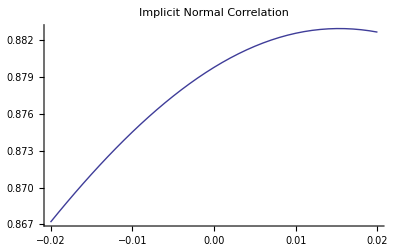
{0.774872,-Graphics-}

```mathematica
Timing[Module[{method="Directe",zetavmethod="Exact",zmethod="Exact",favmethod="Arithmetic",F1=0.0418,α1=0.0435,β1=0.6,ρ1=-0.1819,ν1=0.3798,F2=0.0363,α2=0.0671,β2=0.7,ρ2=-0.1136,ν2=0.3797,T=30,ρs=0.8,ρv=0.5,ρc12=-0.3,ρc21=-0.3,legendrelst=LegendreCoeffs[20]},Print["money=",F1-F2];TestCorrelation[ρ1,ρ2,ρs,ρv,ρc12,ρc21];BiSABRNormalHestonSpreadOptionComputeParameters[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,ρs,ρv,ρc12,ρc21,printflag];strikevalues=Table[k,{k,-0.02,0.02,0.001}];callvalues=Table[BiSABRNormalHestonSpreadOption[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,strikevalues⟦i⟧,T,ρs,ρv,ρc12,ρc21,0],{i,1,Length[strikevalues]}];implicitNormalvols=Table[NormalImplicitVol[F1-F2,strikevalues⟦i⟧,T,callvalues⟦i⟧],{i,1,Length[strikevalues]}];ListPlot[Transpose[{strikevalues,implicitNormalvols}],Joined->True,PlotLabel->"Implicit Normal Vol",PlotRange->All];{σATMnormal1,σATMnormal2}={F1 SABROption[F1,α1,β1,ρ1,ν1,{method,zmethod,zetavmethod,favmethod},F1 1.0001,T]⟦1⟧,F2 SABROption[F2,α2,β2,ρ2,ν2,{method,zmethod,zetavmethod,favmethod},F2 1.0001,T]⟦1⟧};Print["σATMnormal1=",σATMnormal1,"  σATMnormal2=",σATMnormal2];implicitcorrelations=Table[NormalImplicitCorrelation[σATMnormal1,σATMnormal2,implicitNormalvols⟦i⟧],{i,1 Length[strikevalues]}];Print["implicit correlation=",implicitcorrelations];ListPlot[Transpose[{strikevalues,implicitcorrelations}],Joined->True,PlotLabel->"Implicit Normal Correlation",PlotRange->All]]]
```

money=0.0055

Test Correlation : Eigenvalues={2.12284,1.17947,0.562149,0.135538}

α=0.00413158 ν=0.318304 ρ=-0.116659 κ=0.0026302 λ=58582.4 (1.72948×10^-6-0.0000341399 μsp$32710)

σATMnormal1=0.00723631  σATMnormal2=0.00741352

implicit correlation={0.732945,0.736628,0.740275,0.743885,0.747452,0.750972,0.754442,0.757857,0.76121,0.764497,0.767712,0.770846,0.773894,0.776848,0.779699,0.782439,0.785059,0.787549,0.7899,0.792102,0.794145,0.796019,0.797716,0.799227,0.800545,0.801662,0.802573,0.803274,0.803764,0.804041,0.804106,0.803963,0.803615,0.803069,0.80233,0.801407,0.800309,0.799044,0.797622,0.796054,0.794347}

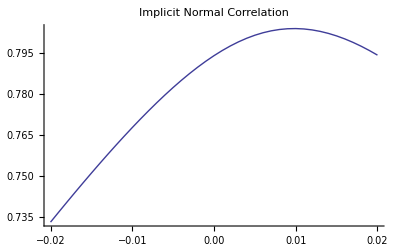
{1.31083,-Graphics-}

```mathematica
Timing[Module[{method="Directe",zetavmethod="Exact",zmethod="Exact",favmethod="Arithmetic",F1=0.0418,α1=0.0435,β1=0.6,ρ1=-0.1819,ν1=0.3798,F2=0.0363,α2=0.0671,β2=0.7,ρ2=-0.1136,ν2=0.3797,T=10,ρs=0.8,ρv=0.5,ρc12=-0.3,ρc21=-0.3,legendrelst=LegendreCoeffs[20]},Print["money=",F1-F2];TestCorrelation[ρ1,ρ2,ρs,ρv,ρc12,ρc21];BiSABRNormalHestonSpreadOptionComputeParameters[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,ρs,ρv,ρc12,ρc21,printflag];strikevalues=Table[k,{k,-0.02,0.02,0.001}];callvalues=Table[BiSABRNormalHestonSpreadOption[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,strikevalues⟦i⟧,T,ρs,ρv,ρc12,ρc21,0],{i,1,Length[strikevalues]}];implicitNormalvols=Table[NormalImplicitVol[F1-F2,strikevalues⟦i⟧,T,callvalues⟦i⟧],{i,1,Length[strikevalues]}];ListPlot[Transpose[{strikevalues,implicitNormalvols}],Joined->True,PlotLabel->"Implicit Normal Vol",PlotRange->All];{σATMnormal1,σATMnormal2}={F1 SABROption[F1,α1,β1,ρ1,ν1,{method,zmethod,zetavmethod,favmethod},F1 1.0001,T]⟦1⟧,F2 SABROption[F2,α2,β2,ρ2,ν2,{method,zmethod,zetavmethod,favmethod},F2 1.0001,T]⟦1⟧};Print["σATMnormal1=",σATMnormal1,"  σATMnormal2=",σATMnormal2];implicitcorrelations=Table[NormalImplicitCorrelation[σATMnormal1,σATMnormal2,implicitNormalvols⟦i⟧],{i,1 Length[strikevalues]}];Print["implicit correlation=",implicitcorrelations];ListPlot[Transpose[{strikevalues,implicitcorrelations}],Joined->True,PlotLabel->"Implicit Normal Correlation",PlotRange->All]]]
```

money=0.0055

Test Correlation : Eigenvalues={2.12284,1.17947,0.562149,0.135538}

Test Correlation : Eigenvalues={1.9095,1.5294,0.491888,0.069216}

Test Correlation : Eigenvalues={1.93078,1.50811,0.470602,0.0905024}

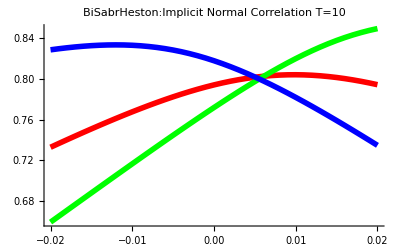
{4.40818,-Graphics-}

```mathematica
Timing[Module[{method="Directe",zetavmethod="Exact",zmethod="Exact",favmethod="Arithmetic",F1=0.0418,α1=0.0435,β1=0.6,ρ1=-0.1819,ν1=0.3798,F2=0.0363,α2=0.0671,β2=0.7,ρ2=-0.1136,ν2=0.3797,T=10,ρs=0.8,ρv=0.5,ρc12=-0.3,ρc21=-0.3,legendrelst=LegendreCoeffs[20]},Print["money=",F1-F2];TestCorrelation[ρ1,ρ2,ρs,ρv,ρc12,ρc21];{σATMnormal1,σATMnormal2}={F1 SABROption[F1,α1,β1,ρ1,ν1,{method,zmethod,zetavmethod,favmethod},F1 1.0001,T]⟦1⟧,F2 SABROption[F2,α2,β2,ρ2,ν2,{method,zmethod,zetavmethod,favmethod},F2 1.0001,T]⟦1⟧};strikevalues=Table[k,{k,-0.02,0.02,0.001}];callvalues=Table[BiSABRNormalHestonSpreadOption[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,strikevalues⟦i⟧,T,ρs,ρv,ρc12,ρc21,0],{i,1,Length[strikevalues]}];implicitNormalvols=Table[NormalImplicitVol[F1-F2,strikevalues⟦i⟧,T,callvalues⟦i⟧],{i,1,Length[strikevalues]}];implicitcorrelations=Table[NormalImplicitCorrelation[σATMnormal1,σATMnormal2,implicitNormalvols⟦i⟧],{i,1 Length[strikevalues]}];ρc12x1=-0.3;ρc21x1=0.3;TestCorrelation[ρ1,ρ2,ρs,ρv,ρc12x1,ρc21x1];callvalues=Table[BiSABRNormalHestonSpreadOption[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,strikevalues⟦i⟧,T,ρs,ρv,ρc12x1,ρc21x1,0],{i,1,Length[strikevalues]}];implicitNormalvols=Table[NormalImplicitVol[F1-F2,strikevalues⟦i⟧,T,callvalues⟦i⟧],{i,1,Length[strikevalues]}];implicitcorrelations2=Table[NormalImplicitCorrelation[σATMnormal1,σATMnormal2,implicitNormalvols⟦i⟧],{i,1 Length[strikevalues]}];ρc12x2=0.3;ρc21x2=-0.3;TestCorrelation[ρ1,ρ2,ρs,ρv,ρc12x2,ρc21x2];callvalues=Table[BiSABRNormalHestonSpreadOption[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,strikevalues⟦i⟧,T,ρs,ρv,ρc12x2,ρc21x2,0],{i,1,Length[strikevalues]}];implicitNormalvols=Table[NormalImplicitVol[F1-F2,strikevalues⟦i⟧,T,callvalues⟦i⟧],{i,1,Length[strikevalues]}];implicitcorrelations3=Table[NormalImplicitCorrelation[σATMnormal1,σATMnormal2,implicitNormalvols⟦i⟧],{i,1 Length[strikevalues]}];ListPlot[{Transpose[{strikevalues,implicitcorrelations}],Transpose[{strikevalues,implicitcorrelations2}],Transpose[{strikevalues,implicitcorrelations3}]},Joined->True,PlotLabel->"BiSabrHeston:Implicit Normal Correlation T="<>ToString[T],PlotRange->All,PlotLegend->{"ρc12="<>ToString[ρc12]<>" ρc21="<>ToString[ρc21],"ρc12="<>ToString[ρc12x1]<>" ρc21="<>ToString[ρc21x1],"ρc12="<>ToString[ρc12x2]<>" ρc21="<>ToString[ρc21x2]},PlotStyle->{{Thickness[0.01],RGBColor[1,0.,0]},{Thickness[0.01],RGBColor[0.,1,0.]},{Thickness[0.01],RGBColor[0,0,1]},{Thickness[0.01],RGBColor[1,0.6,0]},{Thickness[0.01],RGBColor[0,0.5,1]},{Thickness[0.01],RGBColor[0.5,0,1]}}]]]
```

money=0.0055

Test Correlation : Eigenvalues={2.12284,1.17947,0.562149,0.135538}

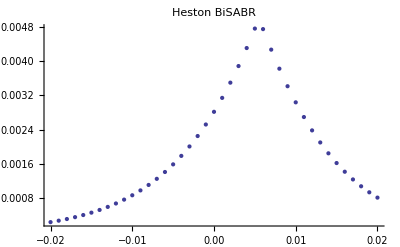

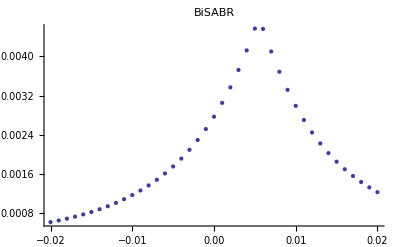

correlation ρ spread=-0.116659

ν spread=0.318304

μ spread=0.00078115

λ spread=58582.4 (1.72948×10^-6-0.0000341399 μsp$87258)

{0.860162,Null}

```mathematica
Timing[Module[{method="Directe",zetavmethod="Exact",zmethod="Exact",favmethod ="Arithmetic",
F1=0.0418,
α1=0.0435,
β1=0.6,
ρ1=-0.1819,
ν1=0.3798,
F2=0.0363,
α2=0.0671,
β2=0.7,
ρ2=-0.1136,
ν2=0.3797,
T=10,
ρs=0.8,
ρv=0.5,
ρc12=-0.3,
ρc21=-0.3,legendrelst=LegendreCoeffs[20],callvalues2},
Print["money=",F1-F2];
TestCorrelation[ρ1,ρ2,ρs,ρv,ρc12,ρc21];
strikevalues=Table[k,{k,-0.020,0.02,0.001}];
callvalues=Table[{strikevalues[[i]],
BiSABRNormalHestonSpreadOption2[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,strikevalues[[i]],T,ρs,ρv,ρc12,ρc21,0]-Max[F1-F2-strikevalues[[i]],0]},{i,1,Length[strikevalues]}];
callvalues2=Table[{strikevalues[[i]],
BiSABRSpreadOption[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,strikevalues[[i]],T,ρs,ρv,ρc12,ρc21,legendrelst,0]-Max[F1-F2-strikevalues[[i]],0]},{i,1,Length[strikevalues]}];
Print[ListPlot[callvalues,PlotLabel->"Heston BiSABR"]];Print[ListPlot[callvalues2,PlotLabel->"BiSABR"]]
Print["correlation ρ spread=",
BiSABRNormalHestonSpreadOptionComputeρ[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,ρs,ρv,ρc12,ρc21,0]];
Print["ν spread=",
BiSABRNormalHestonSpreadOptionComputeν[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,ρs,ρv,ρc12,ρc21,0]];
Print["μ spread=",
BiSABRNormalHestonSpreadOptionComputeμ[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,ρs,ρv,ρc12,ρc21,0]];
Print["λ spread=",
BiSABRNormalHestonSpreadOptionComputeλ[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,ρs,ρv,ρc12,ρc21,0]]]]
```

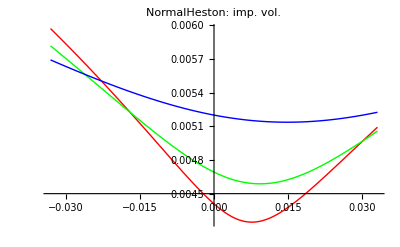
{25.3754,-Graphics-}

```mathematica
Timing[Module[{ρ=-0.11665,λv=0.09975497699499274,StdDev=0.00413158,κ=0.00263019,S0=0.005,V,τ1=3,τ2=10,τ3=30,Vinfini},
V=StdDev^2;Vinfini=κ^2/(2λv);Plot[
{NormalImplicitVol[S0,k,τ1,HestonNormalCall[ρ,λv,Vinfini,κ,V,S0,k,τ1]],
NormalImplicitVol[S0,k,τ2,HestonNormalCall[ρ,λv,Vinfini,κ,V,S0,k,τ2]],
NormalImplicitVol[S0,k,τ3,HestonNormalCall[ρ,λv,Vinfini,κ,V,S0,k,τ3]]},
{k,-8 StdDev,8 StdDev},PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1],RGBColor[0.5,0.5,0.],RGBColor[0,0.5,0.5],RGBColor[0.5,0.,0.5]},PlotLegend->{"T="<>ToString[τ1],"T="<>ToString[τ2],"T="<>ToString[τ3]},LegendPosition->{1,0.},PlotLabel->"NormalHeston: imp. vol."]]]
```

```mathematica
Timing[Module[{method="Directe",zetavmethod="Exact",zmethod="Exact",favmethod="Arithmetic",F1=0.0418,α1=0.0435,β1=0.6,ρ1=-0.1819,ν1=0.3798,F2=0.0363,α2=0.0671,β2=0.7,ρ2=-0.1136,ν2=0.3797,T=10,ρs=0.8,ρv=0.5,ρc12=-0.3,ρc21=-0.3,legendrelst=LegendreCoeffs[20]},Print["money=",F1-F2];TestCorrelation[ρ1,ρ2,ρs,ρv,ρc12,ρc21];{σATMnormal1,σATMnormal2}={F1 SABROption[F1,α1,β1,ρ1,ν1,{method,zmethod,zetavmethod,favmethod},F1 1.0001,T]⟦1⟧,F2 SABROption[F2,α2,β2,ρ2,ν2,{method,zmethod,zetavmethod,favmethod},F2 1.0001,T]⟦1⟧};strikevalues=Table[k,{k,-0.02,0.02,0.001}];callvalues=Table[BiSABRNormalHestonSpreadOption[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,strikevalues⟦i⟧,T,ρs,ρv,ρc12,ρc21,0],{i,1,Length[strikevalues]}];implicitNormalvols=Table[NormalImplicitVol[F1-F2,strikevalues⟦i⟧,T,callvalues⟦i⟧],{i,1,Length[strikevalues]}];implicitcorrelations=Table[NormalImplicitCorrelation[σATMnormal1,σATMnormal2,implicitNormalvols⟦i⟧],{i,1 Length[strikevalues]}];ρc12x1=-0.3;ρc21x1=0.3;TestCorrelation[ρ1,ρ2,ρs,ρv,ρc12x1,ρc21x1];callvalues=Table[BiSABRNormalHestonSpreadOption[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,strikevalues⟦i⟧,T,ρs,ρv,ρc12x1,ρc21x1,0],{i,1,Length[strikevalues]}];implicitNormalvols=Table[NormalImplicitVol[F1-F2,strikevalues⟦i⟧,T,callvalues⟦i⟧],{i,1,Length[strikevalues]}];implicitcorrelations2=Table[NormalImplicitCorrelation[σATMnormal1,σATMnormal2,implicitNormalvols⟦i⟧],{i,1 Length[strikevalues]}];ρc12x2=0.3;ρc21x2=-0.3;TestCorrelation[ρ1,ρ2,ρs,ρv,ρc12x2,ρc21x2];callvalues=Table[BiSABRNormalHestonSpreadOption[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,strikevalues⟦i⟧,T,ρs,ρv,ρc12x2,ρc21x2,0],{i,1,Length[strikevalues]}];implicitNormalvols=Table[NormalImplicitVol[F1-F2,strikevalues⟦i⟧,T,callvalues⟦i⟧],{i,1,Length[strikevalues]}];implicitcorrelations3=Table[NormalImplicitCorrelation[σATMnormal1,σATMnormal2,implicitNormalvols⟦i⟧],{i,1 Length[strikevalues]}];ListPlot[{Transpose[{strikevalues,implicitcorrelations}],Transpose[{strikevalues,implicitcorrelations2}],Transpose[{strikevalues,implicitcorrelations3}]},Joined->True,PlotLabel->"Implicit Normal Correlation",PlotRange->All,PlotLegend->{"ρc12="<>ToString[ρc12]<>" ρc21="<>ToString[ρc21],"ρc12="<>ToString[ρc12x1]<>" ρc21="<>ToString[ρc21x1],"ρc12="<>ToString[ρc12x2]<>" ρc21="<>ToString[ρc21x2]},PlotStyle->{{Thickness[0.01],RGBColor[1,0.,0]},{Thickness[0.01],RGBColor[0.,1,0.]},{Thickness[0.01],RGBColor[0,0,1]},{Thickness[0.01],RGBColor[1,0.6,0]},{Thickness[0.01],RGBColor[0,0.5,1]},{Thickness[0.01],RGBColor[0.5,0,1]}}]];]
```

```mathematica
TestExecution[T_]:=Module[{method="Directe",zetavmethod="Exact",zmethod="Exact",favmethod="Arithmetic",F1=0.0418,α1=0.0435,β1=0.6,ρ1=-0.1819,ν1=0.3798,F2=0.0363,α2=0.0671,β2=0.7,ρ2=-0.1136,ν2=0.3797,ρs=0.8,ρv=0.5,callvalues,implicitNormalvols,strikevalues,k,implicitcorrelations,implicitcorrelations2,implicitcorrelations3,ρc12=-0.3,ρc21=-0.3,ρc12x1=-0.3,ρc21x1=0.3,ρc12x2=0.3,ρc21x2=-0.3,legendrelst=LegendreCoeffs[20]},Print["money=",F1-F2];TestCorrelation[ρ1,ρ2,ρs,ρv,ρc12,ρc21];TestCorrelation[ρ1,ρ2,ρs,ρv,ρc12x1,ρc21x1];TestCorrelation[ρ1,ρ2,ρs,ρv,ρc12x2,ρc21x2];{σATMnormal1,σATMnormal2}={F1 SABROption[F1,α1,β1,ρ1,ν1,{method,zmethod,zetavmethod,favmethod},F1 1.0001,T]⟦1⟧,F2 SABROption[F2,α2,β2,ρ2,ν2,{method,zmethod,zetavmethod,favmethod},F2 1.0001,T]⟦1⟧};strikevalues=Table[k,{k,-0.02,0.02,0.001}];callvalues=Table[BiSABRSpreadOption[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,strikevalues⟦i⟧,T,ρs,ρv,ρc12,ρc21,legendrelst,0],{i,1,Length[strikevalues]}];implicitNormalvols=Table[NormalImplicitVol[F1-F2,strikevalues⟦i⟧,T,callvalues⟦i⟧],{i,1,Length[strikevalues]}];implicitcorrelations=Table[NormalImplicitCorrelation[σATMnormal1,σATMnormal2,implicitNormalvols⟦i⟧],{i,1 Length[strikevalues]}];callvalues=Table[BiSABRSpreadOption[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,strikevalues⟦i⟧,T,ρs,ρv,ρc12x1,ρc21x1,legendrelst,0],{i,1,Length[strikevalues]}];implicitNormalvols=Table[NormalImplicitVol[F1-F2,strikevalues⟦i⟧,T,callvalues⟦i⟧],{i,1,Length[strikevalues]}];implicitcorrelations2=Table[NormalImplicitCorrelation[σATMnormal1,σATMnormal2,implicitNormalvols⟦i⟧],{i,1 Length[strikevalues]}];callvalues=Table[BiSABRSpreadOption[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,strikevalues⟦i⟧,T,ρs,ρv,ρc12x2,ρc21x2,legendrelst,0],{i,1,Length[strikevalues]}];implicitNormalvols=Table[NormalImplicitVol[F1-F2,strikevalues⟦i⟧,T,callvalues⟦i⟧],{i,1,Length[strikevalues]}];implicitcorrelations3=Table[NormalImplicitCorrelation[σATMnormal1,σATMnormal2,implicitNormalvols⟦i⟧],{i,1 Length[strikevalues]}];ListPlot[{Transpose[{strikevalues,implicitcorrelations}],Transpose[{strikevalues,implicitcorrelations2}],Transpose[{strikevalues,implicitcorrelations3}]},Joined->True,PlotLabel->"BiSabr:Implicit Normal Correlation T="<>ToString[T],PlotRange->All,PlotLegend->{"ρc12="<>ToString[ρc12]<>" ρc21="<>ToString[ρc21],"ρc12="<>ToString[ρc12x1]<>" ρc21="<>ToString[ρc21x1],"ρc12="<>ToString[ρc12x2]<>" ρc21="<>ToString[ρc21x2]},PlotStyle->{{Thickness[0.01],RGBColor[1,0.,0]},{Thickness[0.01],RGBColor[0.,1,0.]},{Thickness[0.01],RGBColor[0,0,1]},{Thickness[0.01],RGBColor[1,0.6,0]},{Thickness[0.01],RGBColor[0,0.5,1]},{Thickness[0.01],RGBColor[0.5,0,1]}}];callvalues=Table[BiSABRNormalHestonSpreadOption[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,strikevalues⟦i⟧,T,ρs,ρv,ρc12,ρc21,0],{i,1,Length[strikevalues]}];implicitNormalvols=Table[NormalImplicitVol[F1-F2,strikevalues⟦i⟧,T,callvalues⟦i⟧],{i,1,Length[strikevalues]}];implicitcorrelations=Table[NormalImplicitCorrelation[σATMnormal1,σATMnormal2,implicitNormalvols⟦i⟧],{i,1 Length[strikevalues]}];callvalues=Table[BiSABRNormalHestonSpreadOption[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,strikevalues⟦i⟧,T,ρs,ρv,ρc12x1,ρc21x1,0],{i,1,Length[strikevalues]}];implicitNormalvols=Table[NormalImplicitVol[F1-F2,strikevalues⟦i⟧,T,callvalues⟦i⟧],{i,1,Length[strikevalues]}];implicitcorrelations2=Table[NormalImplicitCorrelation[σATMnormal1,σATMnormal2,implicitNormalvols⟦i⟧],{i,1 Length[strikevalues]}];callvalues=Table[BiSABRNormalHestonSpreadOption[F1,α1,β1,ρ1,ν1,F2,α2,β2,ρ2,ν2,strikevalues⟦i⟧,T,ρs,ρv,ρc12x2,ρc21x2,0],{i,1,Length[strikevalues]}];implicitNormalvols=Table[NormalImplicitVol[F1-F2,strikevalues⟦i⟧,T,callvalues⟦i⟧],{i,1,Length[strikevalues]}];implicitcorrelations3=Table[NormalImplicitCorrelation[σATMnormal1,σATMnormal2,implicitNormalvols⟦i⟧],{i,1 Length[strikevalues]}];ListPlot[{Transpose[{strikevalues,implicitcorrelations}],Transpose[{strikevalues,implicitcorrelations2}],Transpose[{strikevalues,implicitcorrelations3}]},Joined->True,PlotLabel->"BiSabrHeston:Implicit Normal Correlation T="<>ToString[T],PlotRange->All,PlotLegend->{"ρc12="<>ToString[ρc12]<>" ρc21="<>ToString[ρc21],"ρc12="<>ToString[ρc12x1]<>" ρc21="<>ToString[ρc21x1],"ρc12="<>ToString[ρc12x2]<>" ρc21="<>ToString[ρc21x2]},PlotStyle->{{Thickness[0.01],RGBColor[1,0.,0]},{Thickness[0.01],RGBColor[0.,1,0.]},{Thickness[0.01],RGBColor[0,0,1]},{Thickness[0.01],RGBColor[1,0.6,0]},{Thickness[0.01],RGBColor[0,0.5,1]},{Thickness[0.01],RGBColor[0.5,0,1]}}]];
```

money=0.0055

Test Correlation : Eigenvalues={2.12284,1.17947,0.562149,0.135538}

Test Correlation : Eigenvalues={1.9095,1.5294,0.491888,0.069216}

Test Correlation : Eigenvalues={1.93078,1.50811,0.470602,0.0905024}

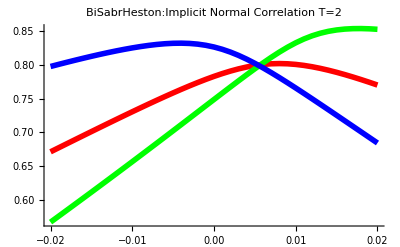

```mathematica
TestExecution[2]
```

```mathematica
TestExecution[10]
```

money=0.0055

Test Correlation : Eigenvalues={2.12284,1.17947,0.562149,0.135538}

Test Correlation : Eigenvalues={1.9095,1.5294,0.491888,0.069216}

Test Correlation : Eigenvalues={1.93078,1.50811,0.470602,0.0905024}

-Graphics-

money=0.0055

Test Correlation : Eigenvalues={2.12284,1.17947,0.562149,0.135538}

Test Correlation : Eigenvalues={1.9095,1.5294,0.491888,0.069216}

Test Correlation : Eigenvalues={1.93078,1.50811,0.470602,0.0905024}

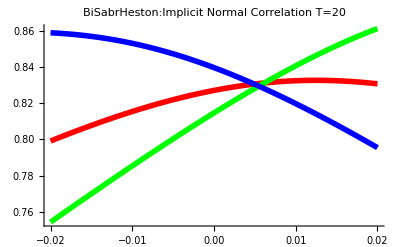

```mathematica
TestExecution[20]
```

money=0.0055

Test Correlation : Eigenvalues={2.12284,1.17947,0.562149,0.135538}

Test Correlation : Eigenvalues={1.9095,1.5294,0.491888,0.069216}

Test Correlation : Eigenvalues={1.93078,1.50811,0.470602,0.0905024}

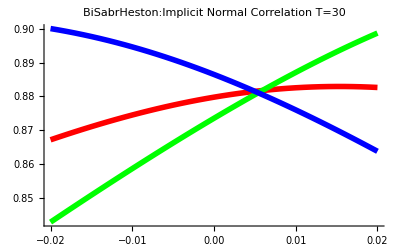

```mathematica
TestExecution[30]
```

money=0.0055

Test Correlation : Eigenvalues={2.12284,1.17947,0.562149,0.135538}

Test Correlation : Eigenvalues={1.9095,1.5294,0.491888,0.069216}

Test Correlation : Eigenvalues={1.93078,1.50811,0.470602,0.0905024}

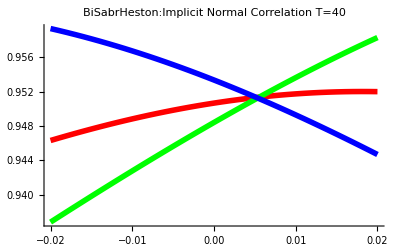

```mathematica
TestExecution[40]
```